```mathematica
a:= 7.56*10^-15
c:= 3*10^10
k:= 0.136
Y:= 0.3
R:= 8.314*10^7
G := 6.67*10^-8
Mstar := 1.4 * (2*10^33)
rstar := 10^6
gz = G * Mstar/rstar^2
```

1.8676×10^14

```mathematica
e3a[p_, rho_] = 5.3*10^21*(rho/10^5)^2*Y^3/((p/(R*rho))/10^8)^3*Exp[-44/(p/(R*rho)/10^8)]
```

(8.22375×10^57 ⅇ^(-(3.65816×10^17 rho)/p) rho^5)/p^3

```mathematica
ecool[p_, rho_,y_]= a*c/(3*k*y^2) * (p/(R*rho))^4
```

(1.16344×10^-35 p^4)/(rho^4 y^2)

```mathematica
sol = NDSolve[{e3a[p[z], rho[z]] == ecool[p[z], rho[z], y[z]], 
y'[z]==-rho[z],
p'[z]/rho[z] == -gz,
p[0]==6.338274548812753*^24,
y[0]==2.6*10^12}, p[z], {z, 0, 10000},PrecisionGoal->20]
```

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

InterpolatingFunction::dmval: Input value {6.83691×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

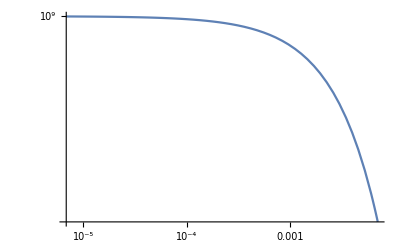

```mathematica
LogLogPlot[rho[z]/.sol, {z, 0, 0.007}, PlotRange->All]
```

```mathematica
FindRoot[e3a[p, 10^9] == ecool[p, 10^9, 2.6*10^12],{p,10^25}]
```

{p→6.33827×10^24}

General::munfl: Exp[-3.65661×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.39555×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.56939×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

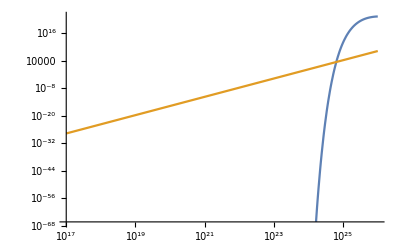

```mathematica
LogLogPlot[{e3a[p, 10^9], ecool[p, 10^9, 2.6*10^12]}, {p, 10^17, 10^26}]
```

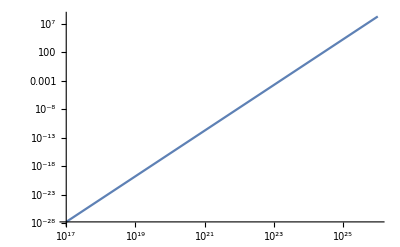

```mathematica
LogLogPlot[ecool[p, 10^9, 2.6*10^12], {p, 10^17, 10^26}]
```

```mathematica
ecool[1, 1, 1]
```

1.16344×10^-35

```mathematica
Series[c1*x^3 Exp[-44*x],{x,0,3}]
```

c1 x^3+O[x]^4

```mathematica
Series[e3a[ p,rho],{p,0,4}]
```

ⅇ^(-(3.65816×10^17 rho)/p+O[p]^5) ((8.22375×10^57 rho^5)/p^3+O[p]^5)

```mathematica
e3aT[t8_, rho_]= 5.3*10^21 * (rho/10^5)^2 * Y^2 * (t8)^3 * Exp[-44*t8]
```

4.77×10^10 ⅇ^(-44 t8) rho^2 t8^3

```mathematica
Series[e3aT[ t,rho],{t,0,4}]
```

4.77×10^10 rho^2 t^3-2.0988×10^12 rho^2 t^4+O[t]^5

```mathematica
e3aAprox[p_, rho_] =5.3*10^21*(rho/10^5)^2*Y^3*(p/(R*rho)/10^8)^-3
```

(8.22375×10^57 rho^5)/p^3

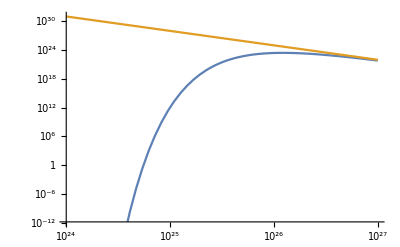

```mathematica
LogLogPlot[{e3a[p, 10^9], e3aAprox[p, 10^9]}, {p, 10^24, 10^27}]
```

```mathematica
e3aAprox[10^26, 10^9]
```

8.22375×10^24

```mathematica
10^26/(R*10^9)
```

1.20279×10^9

```mathematica
(R*10^9)/10^26*10^8
```

0.08314

```mathematica
Plot[e3aAprox[10^8*R*10^9/p, 10^9], {p, 10^23, 10^26}]
```

-Graphics-

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndtola: A component of the solution at z == 0. is essentially zero and the tolerance specified by the AccuracyGoal option could not be achieved.

{{rho[z]→InterpolatingFunction[…][z]}}

InterpolatingFunction::dmval: Input value {0.00976701} lies outside the range of data in the interpolating function. Extrapolation will be used.

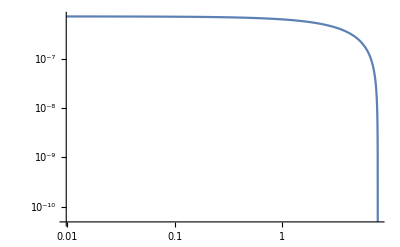

```mathematica
sol = NDSolve[{e3aAprox[p[z], rho[z]] == ecool[p[z], rho[z], y[z]], 
y'[z]==-rho[z],
p'[z]/rho[z] == -gz,
y[0]==2.6*10^12,
rho[0]==10^9}, rho[z], {z, 0, 10000},PrecisionGoal->20]
LogLogPlot[rho[z]/.sol, {z, 0, 10}, PlotRange->All]
```